# Compute the integral for each element of the sum

NB! Note that for M=0 Ξ1 = 0, and for N=0 Ξ2=0. So should be wrapped in a If[M>0, Ξ1, 0] etc.
NB! Be careful with which definition of Ξ has been used, i.e. whether alpha factors are included or not.

Here P = lim (q -> 0) L q' / sqrt (2 α) = beta/(alpha √α)	 (epsilon0_ (n, αB) - epsilon0_ (m, αB)) = beta/alpha^(5/2) (epsilon_n - epsilon_m)
where epsilon0_ (n, αB) is the dimless energy solution to the untilted case .

Note also that the chirality s has not been implemented

## Setup

```mathematica
Ξ1=If[N>=0&& M>0,
If[N>=M-1,
Sqrt[2^N (M-1)!/(2^(M-1) N!)] (-P/Sqrt[2] )^(N-M+1) LaguerreL[M-1, N-M+1,  P^2],
Sqrt[2^(M-1)N!/(2^N(M-1)!)] (P/Sqrt[2] )^(M-N-1) LaguerreL[N, M-N-1, P^2]
 ],
0
]
Ξ2=Ξ1/.{M->N, N->M, P->-P}
```

If[N≥0&&M>0,If[N≥M-1,√((2^N (M-1)!)/(2^(M-1) N!)) (-P/(√2))^(N-M+1) LaguerreL[M-1,N-M+1,P^2],√((2^(M-1) N!)/(2^N (M-1)!)) (P/(√2))^(M-N-1) LaguerreL[N,M-N-1,P^2]],0]

If[M≥0&&N>0,If[M≥N-1,√((2^M (N-1)!)/(2^(N-1) M!)) (--P/(√2))^(M-N+1) LaguerreL[N-1,M-N+1,(-P)^2],√((2^(N-1) M!)/(2^M (N-1)!)) (-P/(√2))^(N-M-1) LaguerreL[M,N-M-1,(-P)^2]],0]

```mathematica
ϵ[m_]:=If[m!=0, tz kappa +Sign[m] α Sqrt[α Abs[m] + kappa^2],(tz-α) kappa]
```

```mathematica
alpha[m_]:=-Sqrt[Abs[m]]/(ϵ[m] - kappa)
```

```mathematica
xi=2*(HeavisideTheta[-ϵ[m]]-HeavisideTheta[-ϵ[n]])/((ϵ[m]-ϵ[n])^2 * (alpha[m]^2+1) *(alpha[n]^2+1));
```

```mathematica
Prule=P->tx(ϵ[m]-ϵ[n])/α^(5/2)
```

P→(tx (If[m≠0,tz kappa+Sign[m] α √(α Abs[m]+kappa^2),(tz-α) kappa]-If[n≠0,tz kappa+Sign[n] α √(α Abs[n]+kappa^2),(tz-α) kappa]))/α^(5/2)

We may use knowledge about which n,m we choose to manually simplify the Heaviside selection factor.

```mathematica
XiProduct=(ϵ[m]+ϵ[n])/α^(3/2)(-alpha[n]^2Ξ2^2 +alpha[m]^2Ξ1^2-tx (alpha[m]Ξ1-alpha[n]Ξ2)(alpha[m]alpha[n](Ξ1/.N->N-1)+(Ξ2/.N->N+1)));
```

And for the T2 product we have

```mathematica
XiProduct2=(
alpha[m] Ξ1 + alpha[n]Ξ2
-tx(alpha[m]alpha[n](Ξ1/.N->N-1)+(Ξ2/.N->N+1))
)×
Sqrt[α](
alpha[m]alpha[n]Sqrt[M-1](Ξ1/.{M->M-1, N->N-1})
+Sqrt[M]Ξ1
-tx Sqrt[M]alpha[n](Ξ2/.M->M-1)
-tx If[M>=2,Sqrt[M-1]alpha[m]^2/alpha[m-1](Ξ1/.M->M-1), 0] (*We must include the If to avoid 1/0 error*)
)/α^2/.{M->Abs[m], N->Abs[n]};
```

This one is pure guess-work.

NBNB make sure to not fuck up m-1 vs M-1!!

```mathematica
XiProduct3=(
alpha[m] Ξ1 + alpha[n]Ξ2
-tx(alpha[m]alpha[n](Ξ1/.N->N-1)+(Ξ2/.N->N+1))
)×
Sqrt[α](
alpha[m]alpha[n]Sqrt[N-1](Ξ2/.{M->M-1, N->N-1})
+Sqrt[N]Ξ2
-tx Sqrt[N]alpha[m](Ξ2/.N->N-1)
-tx Sqrt[N-1]alpha[n]^2/alpha[n-1](Ξ2/.N->N-1)
)/α^2/.{M->Abs[m], N->Abs[n]};
```

```mathematica
stepRule[m_, n_]:=Switch[{m==0, n==0},
{True, True}, 0,
{False, False}, -1,
{True, False}, -HeavisideTheta[-kappa],
{False, True}, -HeavisideTheta[kappa]
]
```

```mathematica
txlist=Subdivide[0,0.5,3];(*{0.,0.01, 0.1, 0.5};*)
numterms=14;
```

## Calculation

```mathematica
kernel = (
XiProduct
- XiProduct2 0
+ XiProduct3 0
);
```

Note the α^2 coming from the normalization factor N*N

```mathematica
mntable=Table[
α^2(xi/.HeavisideTheta[-ϵ[m]]-HeavisideTheta[-ϵ[n]]->stepRule[m,n])kernel Exp[-P^2]/.Prule/.{N->Abs[n], M->Abs[m]}/.α->Sqrt[1-tx^2], 
{m,0,numterms},{n,0, -numterms,-1}];
```

Power::infy: Infinite expression 1/0^2 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

```mathematica
txtable=Table[
mntable/.tz->0
, {tx, txlist}
];
```

```mathematica
integratedmntable=NIntegrate[mntable/.tz->0/.tx->0, {kappa, -Infinity, Infinity}];
integratedmntable[[1]][[1]]=0;
```

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

```mathematica
MatrixPlot[integratedmntable, PlotLegends->Automatic]
```

-Graphics-

```mathematica
integratedmntable//TableForm
```

0 | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.5 | 0. | -0.113706 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.113706 | 0. | -0.0672094 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.0672094 | 0. | -0.0478151 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.0478151 | 0. | -0.037129 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.037129 | 0. | -0.0303533 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.0303533 | 0. | -0.0256714 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.0256714 | 0. | -0.022242 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.022242 | 0. | -0.0196214 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0196214 | 0. | -0.0175536 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0175536 | 0. | -0.0158802 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0158802 | 0. | -0.0144982 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0144982 | 0. | -0.0133376 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0133376 | 0. | -0.0123491
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0123491 | 0.

```mathematica
sum = Table[
Total[Flatten[Take[integratedmntable, i,i]]],
{i, Dimensions[integratedmntable][[1]]}
]
contributions=Differences[sum]
```

{0,-1.,-1.22741,-1.36183,-1.45746,-1.53172,-1.59242,-1.64377,-1.68825,-1.72749,-1.7626,-1.79436,-1.82336,-1.85003,-1.87473}

{-1.,-0.227411,-0.134419,-0.0956303,-0.0742579,-0.0607066,-0.0513429,-0.044484,-0.0392429,-0.0351072,-0.0317604,-0.0289965,-0.0266752,-0.0246981}

## TxTable calculation

```mathematica
integratedtxtable=NIntegrate[txtable/.tz->0, {kappa, -Infinity, Infinity}];
integratedtxtable[[;;,1,1]]=0;
```

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

```mathematica
txtablesum=Table[
Table[Total[Flatten[Take[integratedtxtable[[txindex]], i,i]]],{i, Dimensions[integratedmntable[[txindex]]][[1]]}],
{txindex, Length[integratedtxtable]}
]
```

{{0,-1.,-1.22741,-1.36183,-1.45746,-1.53172,-1.59242,-1.64377,-1.68825,-1.72749,-1.7626,-1.79436,-1.82336,-1.85003,-1.87473},{0,-0.933317,-1.14518,-1.26772,-1.35743,-1.42842,-1.48692,-1.53663,-1.57994,-1.61836,-1.65286,-1.68412,-1.71271,-1.73905,-1.76348},{0,-0.831728,-1.11685,-1.26507,-1.36592,-1.44374,-1.50694,-1.56035,-1.60638,-1.64686,-1.68287,-1.71529,-1.74473,-1.77165,-1.79644},{0,-0.682269,-1.07847,-1.32329,-1.48217,-1.595,-1.68168,-1.75153,-1.81006,-1.86063,-1.9051,-1.94475,-1.98054,-2.01312,-2.04298}}

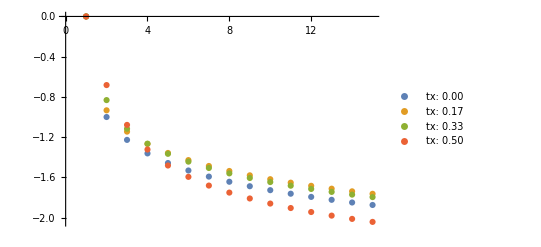

```mathematica
ListPlot[txtablesum, PlotLegends->Map["tx: "<>ToString[DecimalForm[#, {2,2}]]&,  txlist]]
```

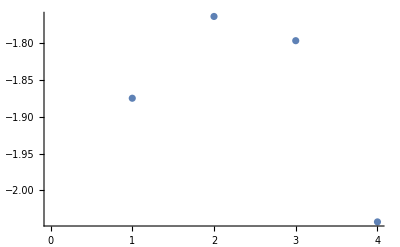

```mathematica
ListPlot[txtablesum[[;;,-1]]]
```

## Lots of mess

```mathematica
Table[Total[Flatten[Take[integratedmntable, i,i]]],{i, Dimensions[integratedmntable][[1]]}]
```

{0,-1.,-1.22741,-1.36183,-1.45746,-1.53172,-1.59242,-1.64377,-1.68825,-1.72749,-1.7626,-1.79436,-1.82336,-1.85003,-1.87473}

```mathematica
integratedtxtable=NIntegrate[txtable/.tz->0, {kappa, -Infinity, Infinity}];
integratedtxtable[[;;,1,1]]=0;
```

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

```mathematica
Table[
Table[Total[Flatten[Take[integratedtxtable[[txindex]], i,i]]],{i, Dimensions[integratedmntable[[txindex]]][[1]]}],
{txindex, Length[integratedtxtable]}
]
```

{{0,-1.,-1.22741,-1.36183,-1.45746,-1.53172,-1.59242,-1.64377,-1.68825,-1.72749,-1.7626,-1.79436,-1.82336,-1.85003,-1.87473},{0,-0.933317,-1.14518,-1.26772,-1.35743,-1.42842,-1.48692,-1.53663,-1.57994,-1.61836,-1.65286,-1.68412,-1.71271,-1.73905,-1.76348},{0,-0.831728,-1.11685,-1.26507,-1.36592,-1.44374,-1.50694,-1.56035,-1.60638,-1.64686,-1.68287,-1.71529,-1.74473,-1.77165,-1.79644},{0,-0.682269,-1.07847,-1.32329,-1.48217,-1.595,-1.68168,-1.75153,-1.81006,-1.86063,-1.9051,-1.94475,-1.98054,-2.01312,-2.04298}}

```mathematica
ListPlot[%, PlotLegends->Map["tx: "<>ToString[DecimalForm[#, {2,2}]]&,  txlist]]
```

-Graphics-

```mathematica
NIntegrate[mntable/.tz->0/.tx->0.4, {kappa, -Infinity, Infinity}];
```

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

```mathematica
%//TableForm
```

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate[Indeterminate,{kappa,-∞,∞}] | -0.390319 | -0.185729 | -0.106445 | -0.0685747 | -0.0481721 | -0.0361523 | -0.028535 | -0.0234037 | -0.0197661 | -0.0170757 | -0.0150151 | -0.0133908 | -0.0120794 | -0.0109996
-0.390319 | 0. | 0.0176497 | 0.0216635 | 0.0115782 | -0.0000813156 | -0.00810895 | -0.0120566 | -0.0130877 | -0.0124743 | -0.0111351 | -0.00961298 | -0.00817875 | -0.00693901 | -0.00591405
-0.185729 | 0.0176497 | 0. | -0.00130054 | -0.000448463 | 0.00509632 | 0.0109242 | 0.0135344 | 0.0124719 | 0.00904626 | 0.00485334 | 0.00103394 | -0.00186246 | -0.00373313 | -0.00472175
-0.106445 | 0.0216635 | -0.00130054 | 0. | 0.00074657 | 0.00126454 | -0.000341148 | -0.00222272 | -0.00212111 | 0.000279642 | 0.0037488 | 0.00677922 | 0.00842596 | 0.00848525 | 0.00727953
-0.0685747 | 0.0115782 | -0.000448463 | 0.00074657 | 0. | -0.000160636 | -0.000271714 | 0.000717638 | 0.00199719 | 0.00209984 | 0.000764384 | -0.00102844 | -0.00206779 | -0.00173128 | -0.000161527
-0.0481721 | -0.0000813156 | 0.00509632 | 0.00126454 | -0.000160636 | 0. | 0.000126933 | 0.000367533 | 0.0000125224 | -0.00063126 | -0.000584302 | 0.000419788 | 0.00167312 | 0.00225116 | 0.00175791
-0.0361523 | -0.00810895 | 0.0109242 | -0.000341148 | -0.000271714 | 0.000126933 | 0. | -0.0000290056 | -0.000134281 | 0.000114519 | 0.000630285 | 0.000740487 | 0.000172 | -0.000585285 | -0.000817
-0.028535 | -0.0120566 | 0.0135344 | -0.00222272 | 0.000717638 | 0.000367533 | -0.0000290056 | 0. | 0.0000286421 | 0.000152076 | 0.0000796302 | -0.00022086 | -0.000291024 | 0.000135338 | 0.000732025
-0.0234037 | -0.0130877 | 0.0124719 | -0.00212111 | 0.00199719 | 0.0000125224 | -0.000134281 | 0.0000286421 | 0. | -1.53846×10^-6 | -0.0000646706 | -0.0000108872 | 0.00023815 | 0.000369045 | 0.000129911
-0.0197661 | -0.0124743 | 0.00904626 | 0.000279642 | 0.00209984 | -0.00063126 | 0.000114519 | 0.000152076 | -1.53846×10^-6 | 0. | 4.73948×10^-6 | 0.0000691959 | 0.0000772158 | -0.0000718451 | -0.000171684
-0.0170757 | -0.0111351 | 0.00485334 | 0.0037488 | 0.000764384 | -0.000584302 | 0.000630285 | 0.0000796302 | -0.0000646706 | 4.73948×10^-6 | 0. | 4.7187×10^-6 | -0.0000287705 | -0.0000343665 | 0.0000883686
-0.0150151 | -0.00961298 | 0.00103394 | 0.00677922 | -0.00102844 | 0.000419788 | 0.000740487 | -0.00022086 | -0.0000108872 | 0.0000691959 | 4.7187×10^-6 | 0. | -1.60733×10^-6 | 0.0000308515 | 0.0000599427
-0.0133908 | -0.00817875 | -0.00186246 | 0.00842596 | -0.00206779 | 0.00167312 | 0.000172 | -0.000291024 | 0.00023815 | 0.0000772158 | -0.0000287705 | -1.60733×10^-6 | 0. | 5.29404×10^-6 | -0.000010032
-0.0120794 | -0.00693901 | -0.00373313 | 0.00848525 | -0.00173128 | 0.00225116 | -0.000585285 | 0.000135338 | 0.000369045 | -0.0000718451 | -0.0000343665 | 0.0000308515 | 5.29404×10^-6 | 0. | -2.77502×10^-6
-0.0109996 | -0.00591405 | -0.00472175 | 0.00727953 | -0.000161527 | 0.00175791 | -0.000817 | 0.000732025 | 0.000129911 | -0.000171684 | 0.0000883686 | 0.0000599427 | -0.000010032 | -2.77502×10^-6 | 0.

```mathematica
tx0values=MapThread[Flatten[{#1, #2}]&, {Flatten[%144], Flatten[Table[{m,n},{m,0,10},{n,-1, -12,-1}], 1]}];
```

MapThread::mptd: Object %144 at position {2, 1} in MapThread[Flatten[{#1,#2}]&,{%144,{{0,-1},{0,-2},{0,-3},{0,-4},{0,-5},{0,-6},{0,-7},{0,-8},{0,-9},{0,-10},«122»}}] has only 0 of required 1 dimensions.

```mathematica
Export[FileNameJoin[{NotebookDirectory[], "tx0.csv"}], tx0values]
```

NotebookDirectory::nosv: The notebook b7e99701-b10a-4453-8be9-7d03debadb52 is not saved.

MapThread::mptd: Object %144 at position {2, 1} in MapThread[Flatten[{#1,#2}]&,{%144,{{0,-1},{0,-2},{0,-3},{0,-4},{0,-5},{0,-6},{0,-7},{0,-8},{0,-9},{0,-10},«122»}}] has only 0 of required 1 dimensions.

Export::chtype: First argument FileNameJoin[{$Failed,tx0.csv}] is not a valid file specification.

$Failed

```mathematica
tx01values=MapThread[Flatten[{#1, #2}]&, {Flatten[%166], Flatten[Table[{m,n},{m,0,10},{n,-1, -12,-1}], 1]}];
```

MapThread::mptd: Object %166 at position {2, 1} in MapThread[Flatten[{#1,#2}]&,{%166,{{0,-1},{0,-2},{0,-3},{0,-4},{0,-5},{0,-6},{0,-7},{0,-8},{0,-9},{0,-10},«122»}}] has only 0 of required 1 dimensions.

```mathematica
Export[FileNameJoin[{NotebookDirectory[], "tx0.1.csv"}], tx01values]
```

NotebookDirectory::nosv: The notebook b7e99701-b10a-4453-8be9-7d03debadb52 is not saved.

MapThread::mptd: Object %166 at position {2, 1} in MapThread[Flatten[{#1,#2}]&,{%166,{{0,-1},{0,-2},{0,-3},{0,-4},{0,-5},{0,-6},{0,-7},{0,-8},{0,-9},{0,-10},«122»}}] has only 0 of required 1 dimensions.

Export::chtype: First argument FileNameJoin[{$Failed,tx0.1.csv}] is not a valid file specification.

$Failed

```mathematica
tx04values=MapThread[Flatten[{#1, #2}]&, {Flatten[%175], Flatten[Table[{m,n},{m,0,10},{n,-1, -12,-1}], 1]}];
```

MapThread::mptd: Object %175 at position {2, 1} in MapThread[Flatten[{#1,#2}]&,{%175,{{0,-1},{0,-2},{0,-3},{0,-4},{0,-5},{0,-6},{0,-7},{0,-8},{0,-9},{0,-10},«122»}}] has only 0 of required 1 dimensions.

```mathematica
Export[FileNameJoin[{NotebookDirectory[], "tx0.4.csv"}], tx01values]
```

NotebookDirectory::nosv: The notebook b7e99701-b10a-4453-8be9-7d03debadb52 is not saved.

MapThread::mptd: Object %166 at position {2, 1} in MapThread[Flatten[{#1,#2}]&,{%166,{{0,-1},{0,-2},{0,-3},{0,-4},{0,-5},{0,-6},{0,-7},{0,-8},{0,-9},{0,-10},«122»}}] has only 0 of required 1 dimensions.

Export::chtype: First argument FileNameJoin[{$Failed,tx0.4.csv}] is not a valid file specification.

$Failed

```mathematica
Flatten[Table[{m,n},{m,0,10},{n,-1, -12,-1}], 1]
```

{{0,-1},{0,-2},{0,-3},{0,-4},{0,-5},{0,-6},{0,-7},{0,-8},{0,-9},{0,-10},{0,-11},{0,-12},{1,-1},{1,-2},{1,-3},{1,-4},{1,-5},{1,-6},{1,-7},{1,-8},{1,-9},{1,-10},{1,-11},{1,-12},{2,-1},{2,-2},{2,-3},{2,-4},{2,-5},{2,-6},{2,-7},{2,-8},{2,-9},{2,-10},{2,-11},{2,-12},{3,-1},{3,-2},{3,-3},{3,-4},{3,-5},{3,-6},{3,-7},{3,-8},{3,-9},{3,-10},{3,-11},{3,-12},{4,-1},{4,-2},{4,-3},{4,-4},{4,-5},{4,-6},{4,-7},{4,-8},{4,-9},{4,-10},{4,-11},{4,-12},{5,-1},{5,-2},{5,-3},{5,-4},{5,-5},{5,-6},{5,-7},{5,-8},{5,-9},{5,-10},{5,-11},{5,-12},{6,-1},{6,-2},{6,-3},{6,-4},{6,-5},{6,-6},{6,-7},{6,-8},{6,-9},{6,-10},{6,-11},{6,-12},{7,-1},{7,-2},{7,-3},{7,-4},{7,-5},{7,-6},{7,-7},{7,-8},{7,-9},{7,-10},{7,-11},{7,-12},{8,-1},{8,-2},{8,-3},{8,-4},{8,-5},{8,-6},{8,-7},{8,-8},{8,-9},{8,-10},{8,-11},{8,-12},{9,-1},{9,-2},{9,-3},{9,-4},{9,-5},{9,-6},{9,-7},{9,-8},{9,-9},{9,-10},{9,-11},{9,-12},{10,-1},{10,-2},{10,-3},{10,-4},{10,-5},{10,-6},{10,-7},{10,-8},{10,-9},{10,-10},{10,-11},{10,-12}}

```mathematica
MatrixPlot[integratedmntable, PlotLegends->Automatic]
```

-Graphics-

```mathematica
MatrixPlot[Transpose[%], PlotLegends->Automatic]
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Function::slot: Slot[«1»] (in Blend[System`PlotThemeDump`$ThemeDefaultMatrix,Slot[«1»]]&) should contain a non-negative integer or string.

MatrixPlot::mat0: Argument … at position 1 is not a matrix.

MatrixPlot[Transpose[-Graphics-],PlotLegends→Automatic]

```mathematica
Table[Total[Flatten[Take[%111, i,i]]],{i, 11}]
```

Take::take: Cannot take positions 1 through 1 in 111.

Take::take: Cannot take positions 1 through 2 in %111.

Take::take: Cannot take positions 1 through 3 in %111.

General::stop: Further output of Take::take will be suppressed during this calculation.

{Total[Take[%111,1,1]],Total[Take[%111,2,2]],Total[Take[%111,3,3]],Total[Take[%111,4,4]],Total[Take[%111,5,5]],Total[Take[%111,6,6]],Total[Take[%111,7,7]],Total[Take[%111,8,8]],Total[Take[%111,9,9]],Total[Take[%111,10,10]],Total[Take[%111,11,11]]}

```mathematica
Differences[%128]
```

Differences[%128]

```mathematica
MatrixPlot[Transpose[PadLeft[%23]], PlotLegends->Automatic]
```

-Graphics-

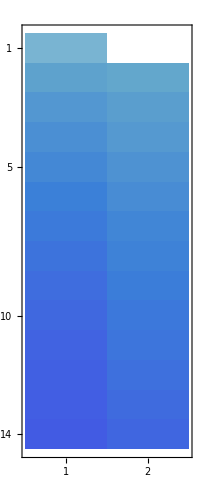

```mathematica
MatrixPlot[
Drop[
LowerTriangularize[Transpose[PadLeft[%23]], -1],
1, -2]
]
```

```mathematica
MatrixPlot[Transpose[PadRight[%86]], PlotLegends->Automatic]
```

MatrixPlot::mat0: Argument Transpose[PadRight[%86]] at position 1 is not a matrix.

MatrixPlot[Transpose[PadRight[%86]],PlotLegends→Automatic]

```mathematica
MatrixPlot[%]
```

MatrixPlot::mat0: Argument Transpose[PadRight[%86]] at position 1 is not a matrix.

MatrixPlot::mat0: Argument MatrixPlot[Transpose[PadRight[%86]],PlotLegends→Automatic] at position 1 is not a matrix.

MatrixPlot[MatrixPlot[Transpose[PadRight[%86]],PlotLegends→Automatic]]

```mathematica
%
```

MatrixPlot::mat0: Argument Transpose[PadRight[%86]] at position 1 is not a matrix.

MatrixPlot::mat0: Argument MatrixPlot[Transpose[PadRight[%86]],PlotLegends→Automatic] at position 1 is not a matrix.

MatrixPlot[MatrixPlot[Transpose[PadRight[%86]],PlotLegends→Automatic]]

```mathematica
MatrixPlot[%113, PlotLegends->Automatic]
```

MatrixPlot::mat0: Argument %113 at position 1 is not a matrix.

MatrixPlot[%113,PlotLegends→Automatic]

```mathematica
Total[%, {2}]Ξ2/.N->N-1, M->M-1)
```

```mathematica
Ξ2/.N->N-1, M->M-1)
```

```mathematica
ListPlot[-Accumulate[%]*4]
```

MatrixPlot::mat0: Argument %113 at position 1 is not a matrix.

ListPlot::lpn: -4. MatrixPlot[%113,%113+(PlotLegends→Automatic)] is not a list of numbers or pairs of numbers.

ListPlot[-4 MatrixPlot[%113,%113+(PlotLegends→Automatic)]]

```mathematica
ListPlot[-Accumulate[%]*4]
```

MatrixPlot::argt: MatrixPlot called with 2 arguments; 0 or 1 arguments are expected.

ListPlot::lpn: -4. MatrixPlot[%113,%113+(PlotLegends→Automatic)] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[-4 ListPlot[-4 MatrixPlot[%113,%113+(PlotLegends→Automatic)]]]

```mathematica
MatrixPlot[PadLeft[%]]
```

MatrixPlot::argt: MatrixPlot called with 2 arguments; 0 or 1 arguments are expected.

ListPlot::lpn: -4. MatrixPlot[%113,%113+(PlotLegends→Automatic)] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

MatrixPlot::mat0: Argument PadLeft[ListPlot[-4 ListPlot[-4 MatrixPlot[%113,Out[«1»]+Rule[«2»]]]]] at position 1 is not a matrix.

MatrixPlot[PadLeft[ListPlot[-4 ListPlot[-4 MatrixPlot[%113,%113+(PlotLegends→Automatic)]]]]]

```mathematica
MatrixPlot[%]
```

MatrixPlot::argt: MatrixPlot called with 2 arguments; 0 or 1 arguments are expected.

ListPlot::lpn: -4. MatrixPlot[%113,%113+(PlotLegends→Automatic)] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

MatrixPlot::mat0: Argument PadLeft[ListPlot[-4 ListPlot[-4 MatrixPlot[%113,Out[«1»]+Rule[«2»]]]]] at position 1 is not a matrix.

MatrixPlot::mat0: Argument MatrixPlot[PadLeft[ListPlot[-4 ListPlot[-4 MatrixPlot[Out[«1»],Plus[«2»]]]]]] at position 1 is not a matrix.

MatrixPlot[MatrixPlot[PadLeft[ListPlot[-4 ListPlot[-4 MatrixPlot[%113,%113+(PlotLegends→Automatic)]]]]]]